## Barbosa kappa func

```mathematica
normK[V_,kappa_]:=1/(π^(3/2)(2-3/kappa)^(3/2))(kappa^(3/2)/2 Gamma[kappa-1/2]/Gamma[kappa+1]+V/((2-3/kappa)^(1/2)π^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-V^2/(2kappa -3)])^-1
barbKappa[vpar_,vperp_,V_,alpha_,kappa_]:=normK[V,kappa] (1+(vpar^2+vperp^2+V^2-2 V(vpar^2+vperp^2(1-alpha))^(1/2))/(2 kappa - 3))^(-(kappa+1))UnitStep[vpar]
```

## α = 0 (all mirroring)

```mathematica
alpha=0.0;
vbeam=3.5;
```

```mathematica
Plot3D[barbKappa[vz,vperp,vbeam,alpha,40],{vz,0,10},{vperp,-5,5},PlotRange->All,PlotPoints->80]
```

-Graphics3D-

```mathematica
Plot3D[barbKappa[vz,vperp,vbeam,alpha,30],{vz,0,10},{vperp,-10,10},PlotRange->All,ImageSize->900,PlotPoints->80]
```

-Graphics3D-

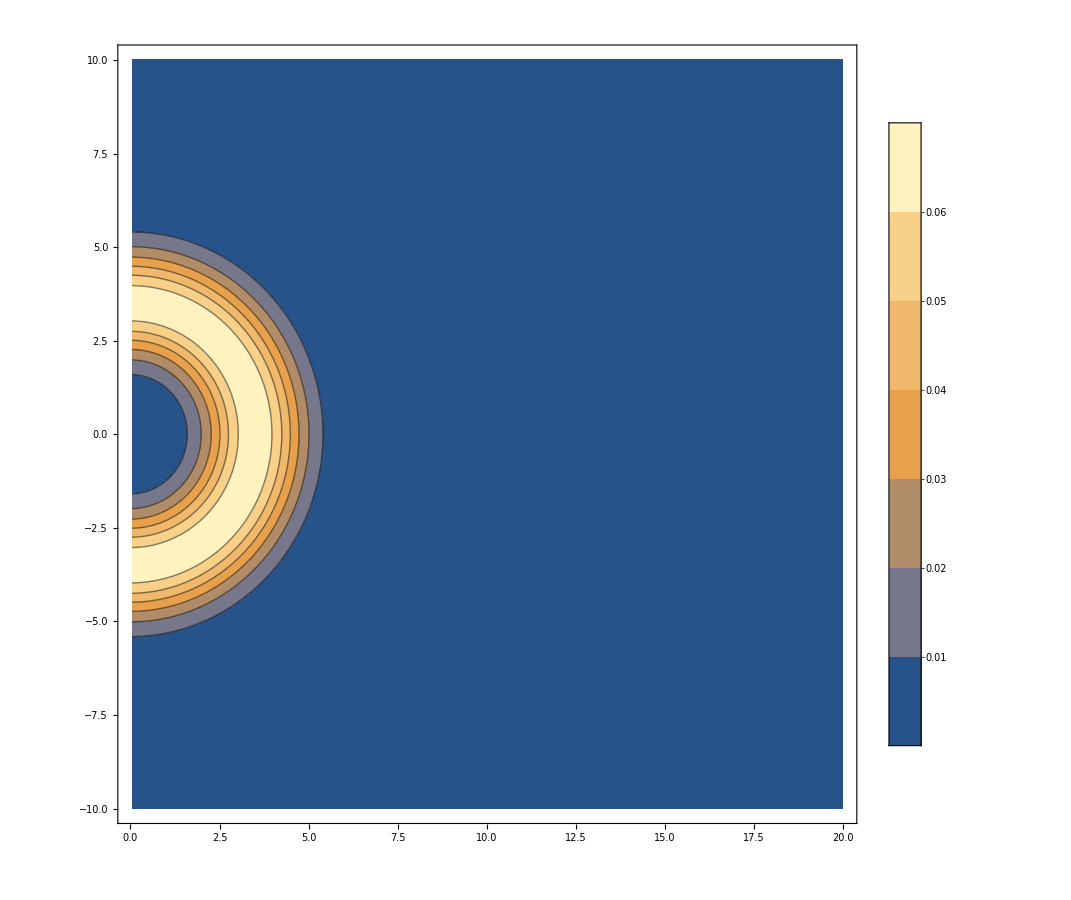

```mathematica
ContourPlot[barbKappa[vz,vperp,vbeam,alpha,30],{vz,0,20},{vperp,-10,10},PlotRange->All,ImageSize->900,PlotLegends->Automatic,PlotPoints->80]
```

```mathematica
Plot3D[barbKappa[vz,vperp,vbeam,alpha,4],{vz,0,10},{vperp,-10,10},PlotRange->All,ImageSize->900,PlotPoints->70]
```

-Graphics3D-

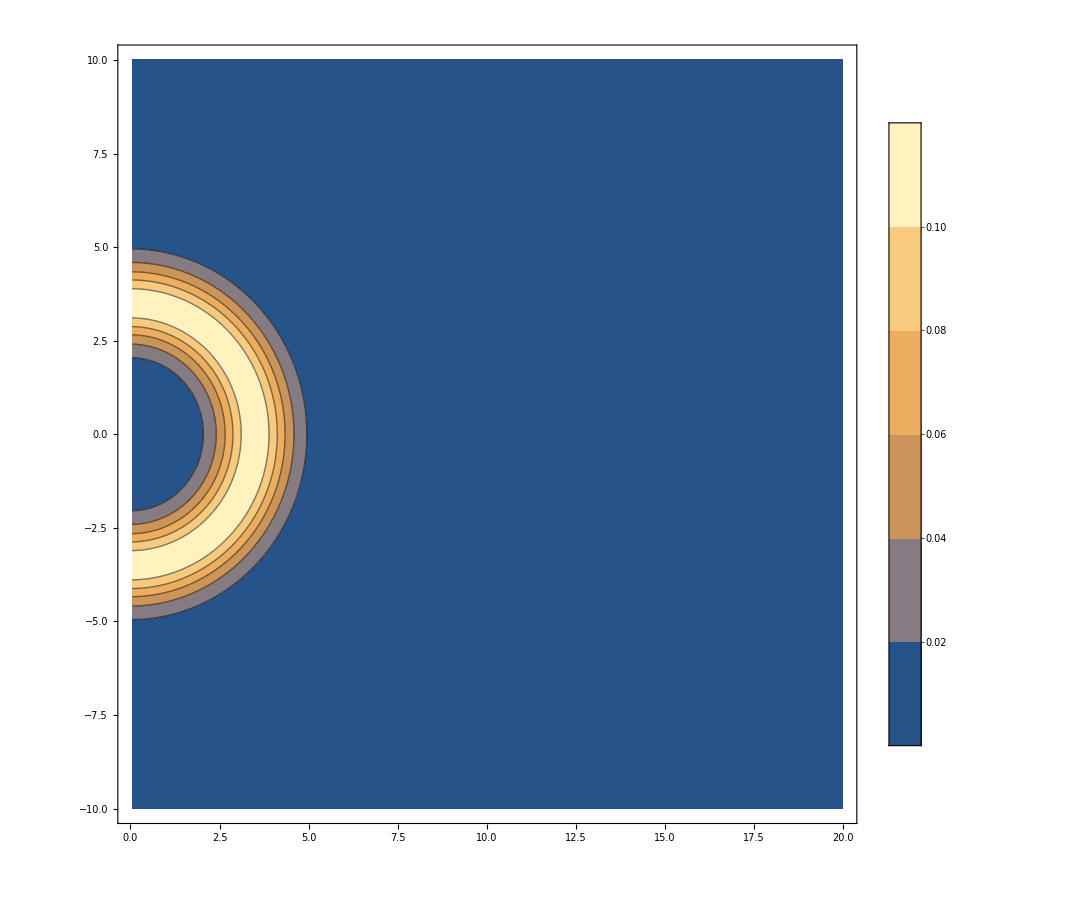

```mathematica
ContourPlot[barbKappa[vz,vperp,vbeam,alpha,4],{vz,0,20},{vperp,-10,10},PlotRange->All,ImageSize->900,PlotLegends->Automatic,PlotPoints->80]
```

```mathematica
Plot3D[barbKappa[vz,vperp,vbeam,alpha,2],{vz,0,10},{vperp,-10,10},PlotRange->All,ImageSize->900,PlotPoints->70]
```

-Graphics3D-

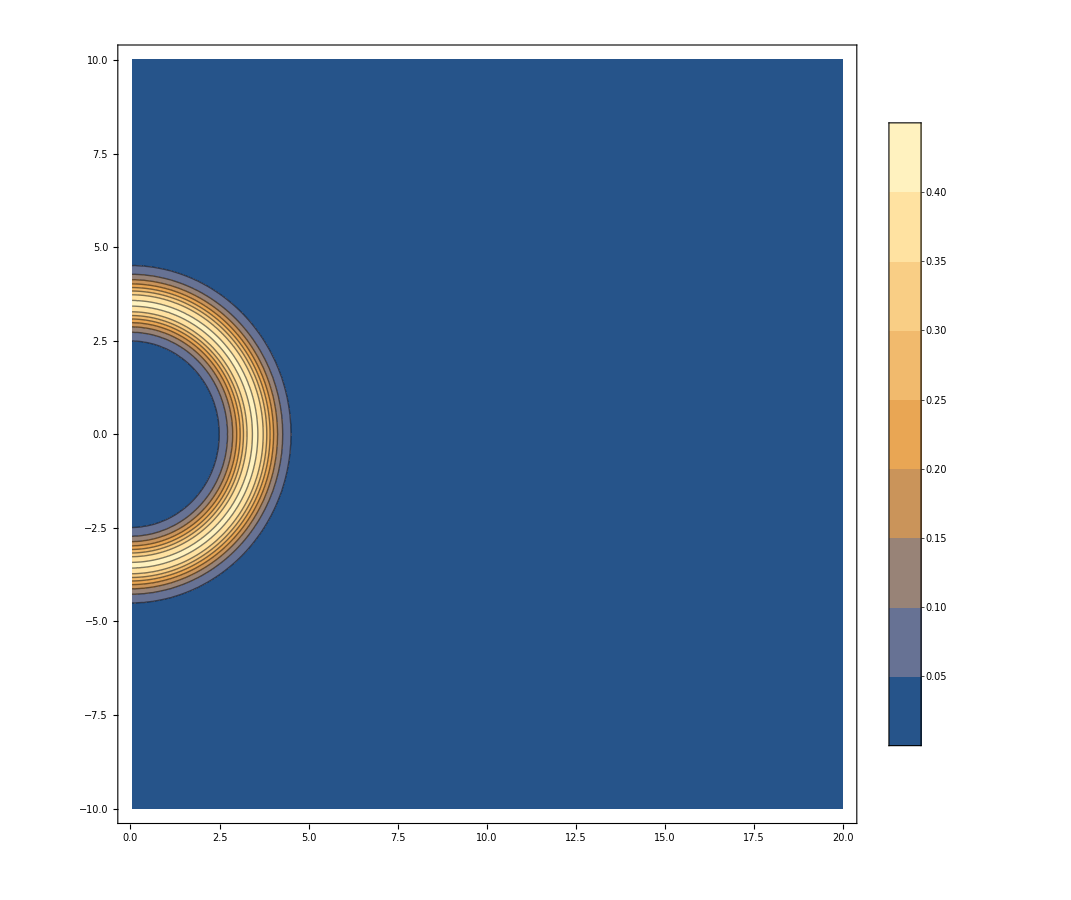

```mathematica
ContourPlot[barbKappa[vz,vperp,vbeam,alpha,2],{vz,0,20},{vperp,-10,10},PlotRange->All,ImageSize->900,PlotLegends->Automatic,PlotPoints->80]
```

```mathematica
ContourPlot[barbKappa[vz,vperp,vbeam,alpha,1.6],{vz,0,20},{vperp,-10,10},PlotRange->All,ImageSize->900,PlotLegends->Automatic,PlotPoints->80]
```

-Graphics-